### Plots showing the relative error of a stirling approximation.

```mathematica
<<peeters`;
peeters`setGitDir["../project/figures/phy452-basicstatmech"]
```

/Users/pjoot/project/figures/phy452-basicstatmech

√(2 π) ⅇ^-n n^(n+1/2)

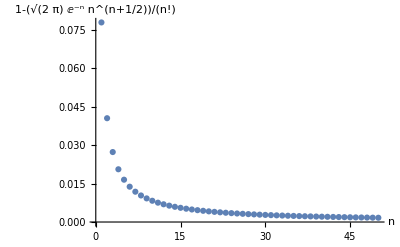

0.922137

```mathematica
Clear[stirling, plot]
stirling[N_] = Sqrt[2 Pi N] N^N E^(-N) ;
stirling[n] // TraditionalForm
plot = Module[{s,f, r, p},
r = 50 ;
s = Table[{n, stirling[n]}, {n, 1, r}] // N ;
f = Table[{n, Factorial[n]}, {n, 1, r}] // N  ;
d = Table[(Factorial[n] - stirling[n])/Factorial[n], {n, 1, r}]  // N ;
 p = ListPlot[d, 
PlotRange -> Full,
PlotStyle->Thick,
 AxesLabel->{n,1 -stirling[n]/n!}] ;
(* {d, p} *)
p
]
stirling[1] // N
```

```mathematica
SetDirectory["C:\\Users\\Peeter\\cygwin_home\\physicsplay\\notes\\phy452\\figures"]
```

C:\Users\Peeter\cygwin_home\physicsplay\notes\phy452\figures

```mathematica
peeters`exportForLatex["stirlingErrorFig3", plot]
```

{C:\Users\Peeter\cygwin_home\physicsplay\notes\phy452\figures/stirlingError.eps,C:\Users\Peeter\cygwin_home\physicsplay\notes\phy452\figures/stirlingErrorpn.png}